```mathematica
SetDirectory["/home/data/mg5213/Downloads"]
```

/home/data/mg5213/Downloads

```mathematica
da=ReadList["hydra_matterpower_z0.dat",{Number,Number}];
kCAMB=Flatten[Drop[da,{},{2,2}]];
PkCAMB=Flatten[Drop[da,{},{1,1}]];
PlinHydra=Interpolation[da];
```

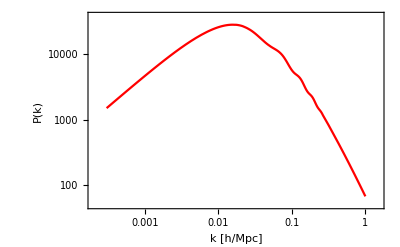

```mathematica
LogLogPlot[PlinHydra[k],{k,0.0003,1},Frame->True,PlotStyle->Red,LabelStyle->{Italic,FontFamily->"Helvetica"},FrameLabel->{"k [h/Mpc]","P(k)"},ColorFunctionScaling->False,ImageSize->400,FrameTicksStyle->20,FrameStyle->21]
```

```mathematica
L=100;
Ng = 0;
Do[Do[Do[If[(i-L/2)^2+(j-L/2)^2+(k-L/2)^2<(L/2)^2,Ng++],{k,L}],{j,L}],{i,L}];
Ng
```

523155

```mathematica
J[k1_,k2_] := 1/Ng^3
```